## Fermions+ condensate

```mathematica
Clear[g,c1,c2]
```

```mathematica
U[t_]=c1 JacobiSN[c1(t+c2),-1]
```

c1 JacobiSN[c1 (c2+t),-1]

```mathematica
g=0.5;c1=1;c2=1;
```

```mathematica
U[t]
```

JacobiSN[0.5 (1+t),-1]

```mathematica
(*For Subscript[ψ, 1L1] and Subscript[ψ, 2L2]*)
```

```mathematica
DSolve[ D[p[t],t]+I/2 g U[t]p[t]==0,p,t]
```

{{p→Function[{t},ⅇ^(1/2 ⅈ ArcTan[JacobiCD[c1 g (c2+t),-1]]) C[1]]}}

```mathematica
(*Maple solution*)
```

```mathematica
p[t_]=1/(√(JacobiDN[c1(t+c2),-1]-I JacobiCN[c1(t+c2),-1]));
```

```mathematica
D[p[t],t]+I/2 U[t]p[t]//Simplify
```

0

```mathematica
(*Initial conditions for both functions*)
```

```mathematica
N[1/(√(JacobiDN[0,-1]-I JacobiCN[0,-1]))]
```

0.776887+0.321797 ⅈ

```mathematica
N[ⅇ^(1/2 ⅈ ArcTan[JacobiCD[ 0,-1]])]
```

0.92388+0.382683 ⅈ

```mathematica
(*Plots for both solutions(For comparision)*)
```

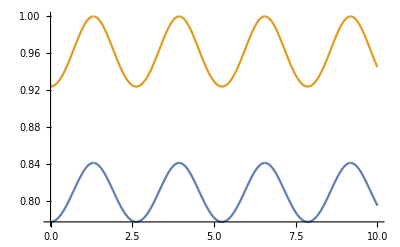

```mathematica
Plot[{Re[1/(√(JacobiDN[t,-1]-I JacobiCN[t,-1]))],Re[ⅇ^(1/2 ⅈ ArcTan[JacobiCD[ t,-1]])]},{t,0,10}]
```

```mathematica
(* For Subscript[ψ, 1L2],Subscript[ψ, 2L1]*)
```

```mathematica
eqns={I D[q[t],t]-  u[t]r[t]+1/2 u[t]q[t]==0,I D[r[t],t]- u[t]q[t]+1/2 u[t]r[t]==0};
```

```mathematica
DSolve[eqns,{q,r},t]
```

DSolve[{1/2 g JacobiSN[g t,-1] q[t]-g JacobiSN[g t,-1] r[t]+ⅈ q'[t]==0,-g JacobiSN[g t,-1] q[t]+1/2 g JacobiSN[g t,-1] r[t]+ⅈ r'[t]==0},{q,r},t]

```mathematica
(*Maple solutions*)
```

```mathematica
q1[t_]=c3(JacobiDN[ c1(t+c2),-1]-I JacobiCN[ c1(t+c2),-1])^(3/2)+c4(JacobiDN[c1(t+c2),-1]-I JacobiCN[ c1(t+c2),-1])^(-1/2);
```

```mathematica
r1[t_]=-c3(JacobiDN[ c1 (t+c2),-1]-I JacobiCN[c1(t+c2),-1])^(3/2)+c4(JacobiDN[ c1(t+c2),-1]-I JacobiCN[ c1(t+c2),-1])^(-1/2);
```

```mathematica
I D[q1[t],t]-  U[t]r1[t]+1/2 U[t]q1[t]//FullSimplify
```

0

```mathematica
I D[r1[t],t]-  U[t]q1[t]+1/2 U[t]r1[t]//FullSimplify
```

0

```mathematica
(*PLots-bilinears*)
```

```mathematica
c1=1;c2=0;g=0.333;
```

```mathematica
r1[t]
```

-(-ⅈ JacobiCN[0.333 t,-1]+JacobiDN[0.333 t,-1])^(3/2)

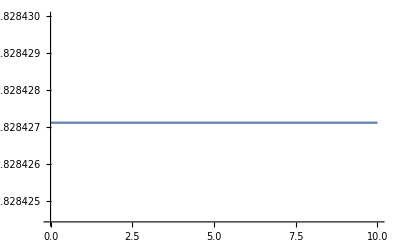

```mathematica
Plot[r1[t]Conjugate[r1[t]],{t,0,10},PlotRange->{Full,{2.82842444,2.82843}}]
```

```mathematica
Plot3D[JacobiSN[0.5(t+1),-1],{t,0,20},{z,0,20},AxesLabel->{"t","z","U"},ColorFunction->Function[{z,t,y},Hue[0.7y]]]
```

-Graphics3D-

```mathematica
(*Bilinear plots*)
```

```mathematica
JacobiSN[√2(1/2),-1]//N
```

0.68979

```mathematica
4 EllipticK[-1]/(√2(0.6897897672064442))//N
```

5.37577

```mathematica
Λ[t_]=JacobiDN[ gym c1(t+c2),-1]-I JacobiCN[gym  c1(t+c2),-1];
psi1L1[t_]=A1 Λ[t]^(-1/2);
psi1L2[t_]=c3 Λ[t]^(3/2)+c4 Λ[t]^(-1/2);
psi2L2[t_]=A2 Λ[t]^(-1/2);
psi2L1[t_]=-c3 Λ[t]^(3/2)+c4 Λ[t]^(-1/2);
```

```mathematica
gym=0.5;c1=1;c2=0;A1=0;A2=0;c3=1;c4=1;
```

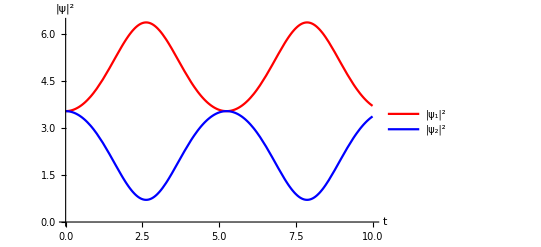

```mathematica
Plot[{(Conjugate[psi1L1[t]]psi1L1[t]+Conjugate[psi1L2[t]]psi1L2[t]),(Conjugate[psi2L1[t]]psi2L1[t]+Conjugate[psi2L2[t]]psi2L2[t])},{t,0,10},PlotStyle->{Red, Blue}, AxesLabel->{"t","|ψ|^2"},PlotLegends->{"|ψ_1|^2","|ψ_2|^2"}]
```

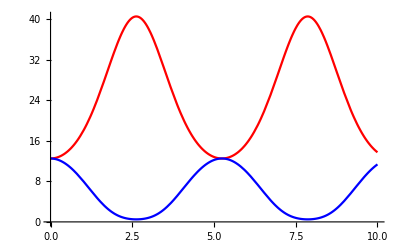

```mathematica
Plot[{(Conjugate[psi1L1[t]]psi1L1[t]+Conjugate[psi1L2[t]]psi1L2[t])^2,(Conjugate[psi2L1[t]]psi2L1[t]+Conjugate[psi2L2[t]]psi2L2[t])^2},{t,0,10},PlotStyle->{Red, Blue}]
```

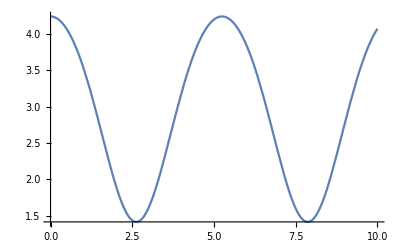

```mathematica
Plot[Conjugate[psi2L1[t]]psi2L1[t]+Conjugate[psi2L2[t]]psi2L2[t],{t,0,10}]
```

```mathematica
Plot[Conjugate[psi1L1[t]]psi1L1[t]+Conjugate[psi1L2[t]]psi1L2[t]+Conjugate[psi2L1[t]]psi2L1[t]+Conjugate[psi2L2[t]]psi2L2[t],{t,0,10}]
```

-Graphics-